```mathematica
(*dessins pour l'article
Plus gros ellipsoides inclus.
déjà fait.
*)
```

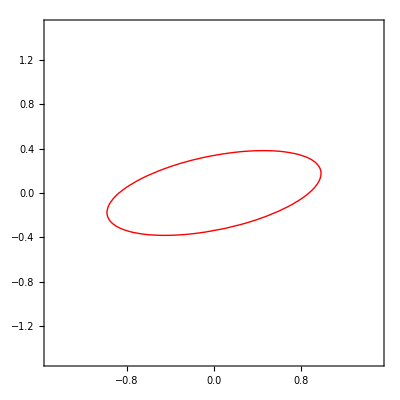

```mathematica
(*famille croissante des ellipsoides*)
R={{Cos[#],Sin[#]},{-Sin[#],Cos[#]}}&;
M[theta_,lambda1_,lambda2_]:=Transpose[R[theta]].{{lambda1,0},{0,lambda2}}.R[theta];
M[theta_,lambda1_,lambda2_,alpha_]:=Transpose[R[theta]].{{Max[lambda1,alpha],0},{0,Max[lambda2,alpha]}}.R[theta];
TEll = Table[{x,y}.M[0.2,1,9,alpha].{x,y}==1,{alpha,1,9}];

ContourPlot[{x,y}.M[0.2,1,9].{x,y}==1,{x,-1.5,1.5},{y,-1.5,1.5},AspectRatio->1,ContourStyle->Red]
```

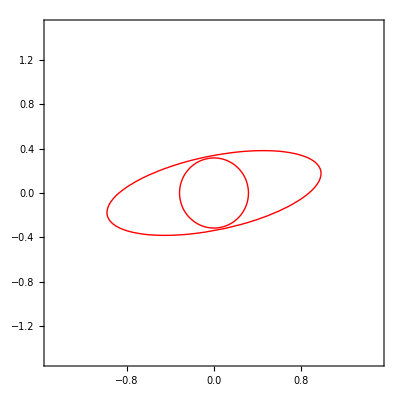

```mathematica
ContourPlot[{{x,y}.M[0.2,1,9].{x,y}==1,{x,y}.M[0.2,1,9,10].{x,y}==1},{x,-1.5,1.5},{y,-1.5,1.5},AspectRatio->1,ContourStyle->Red]
```

```mathematica
Prepend[Table[{x,y}.M[0.2,1,9,1/r^2].{x,y}==1,{r,0.1,0.9,0.1}],{x,y}.M[0.2,1,9].{x,y}==1]
```

{x (1.31576 x-1.55767 y)+y (-1.55767 x+8.68424 y)==1,x (100. x+0. y)+y (0. x+100. y)==1,x (25. x+0. y)+y (0. x+25. y)==1,x (11.1111 x+4.44089×10^-16 y)+y (-4.44089×10^-16 x+11.1111 y)==1,x (6.35854 x-0.53545 y)+y (-0.53545 x+8.89146 y)==1,x (4.19735 x-0.973546 y)+y (-0.973546 x+8.80265 y)==1,x (3.02337 x-1.21152 y)+y (-1.21152 x+8.75441 y)==1,x (2.31549 x-1.35502 y)+y (-1.35502 x+8.72532 y)==1,x (1.85605 x-1.44815 y)+y (-1.44815 x+8.70645 y)==1,x (1.54107 x-1.512 y)+y (-1.512 x+8.6935 y)==1}

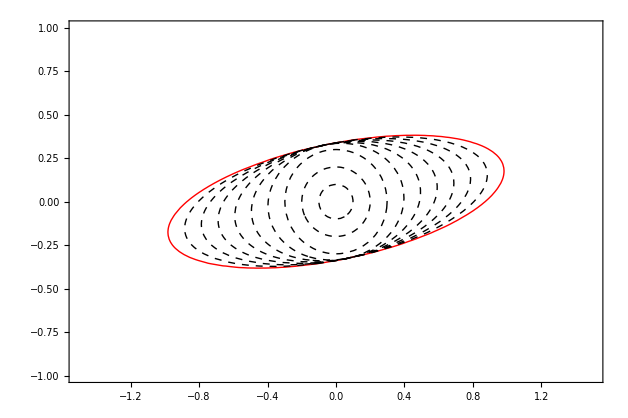

```mathematica
ContourPlot[{x (1.3157560239884596 x-1.557673369234602 y)+y (-1.557673369234602 x+8.68424397601154 y)==1,x (99.99999999999997 x+0. y)+y (0. x+99.99999999999997 y)==1,x (24.999999999999993 x+0. y)+y (0. x+24.999999999999993 y)==1,x (11.111111111111109 x+4.440892098500626*^-16 y)+y (-4.440892098500626*^-16 x+11.111111111111109 y)==1,x (6.358541133246032 x-0.5354502206743947 y)+y (-0.5354502206743947 x+8.891458866753968 y)==1,x (4.197347514992788 x-0.9735458557716263 y)+y (-0.9735458557716263 x+8.802652485007213 y)==1,x (3.023365796435468 x-1.2115237316269127 y)+y (-1.211523731626913 x+8.75441198134231 y)==1,x (2.3154918473981243 x-1.355016884971937 y)+y (-1.355016884971937 x+8.725324479132489 y)==1,x (1.8560544285517708 x-1.4481494604602942 y)+y (-1.4481494604602942 x+8.70644557144823 y)==1,x (1.5410656467418846 x-1.5120008476058098 y)+y (-1.5120008476058098 x+8.693502254492683 y)==1},

{x,-1.5,1.5},{y,-1,1},AspectRatio->2/3,ContourStyle->Prepend[Array[Dashed&,14],Red]]
```

```mathematica
Prepend[Table[{x,y}.M[0.2,1,9,1/r^2].{x,y}==1,{r,0.1,1,0.1}],Abs[{x,y}.M[0.2,-1,9].{x,y}]==1]
```

{Abs[x (-0.605305 x-1.94709 y)+y (-1.94709 x+8.6053 y)]==1,x (100. x+0. y)+y (0. x+100. y)==1,x (25. x+0. y)+y (0. x+25. y)==1,x (11.1111 x+4.44089×10^-16 y)+y (-4.44089×10^-16 x+11.1111 y)==1,x (6.35854 x-0.53545 y)+y (-0.53545 x+8.89146 y)==1,x (4.19735 x-0.973546 y)+y (-0.973546 x+8.80265 y)==1,x (3.02337 x-1.21152 y)+y (-1.21152 x+8.75441 y)==1,x (2.31549 x-1.35502 y)+y (-1.35502 x+8.72532 y)==1,x (1.85605 x-1.44815 y)+y (-1.44815 x+8.70645 y)==1,x (1.54107 x-1.512 y)+y (-1.512 x+8.6935 y)==1,x (1.31576 x-1.55767 y)+y (-1.55767 x+8.68424 y)==1}

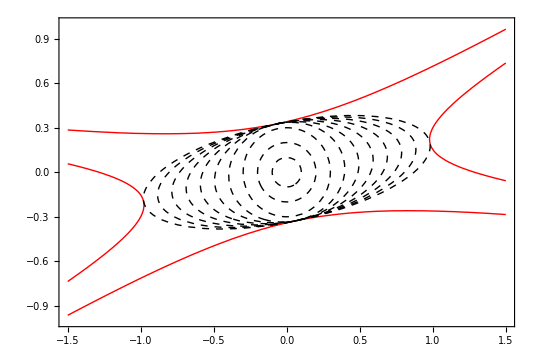

```mathematica
ContourPlot[{Abs[x (-0.6053049700144254 x-1.9470917115432524 y)+y (-1.9470917115432524 x+8.605304970014426 y)]==1,x (99.99999999999997 x+0. y)+y (0. x+99.99999999999997 y)==1,x (24.999999999999993 x+0. y)+y (0. x+24.999999999999993 y)==1,x (11.111111111111109 x+4.440892098500626*^-16 y)+y (-4.440892098500626*^-16 x+11.111111111111109 y)==1,x (6.358541133246032 x-0.5354502206743947 y)+y (-0.5354502206743947 x+8.891458866753968 y)==1,x (4.197347514992788 x-0.9735458557716263 y)+y (-0.9735458557716263 x+8.802652485007213 y)==1,x (3.023365796435468 x-1.2115237316269127 y)+y (-1.211523731626913 x+8.75441198134231 y)==1,x (2.3154918473981243 x-1.355016884971937 y)+y (-1.355016884971937 x+8.725324479132489 y)==1,x (1.8560544285517708 x-1.4481494604602942 y)+y (-1.4481494604602942 x+8.70644557144823 y)==1,x (1.5410656467418846 x-1.5120008476058098 y)+y (-1.5120008476058098 x+8.693502254492683 y)==1,x (1.3157560239884596 x-1.557673369234602 y)+y (-1.557673369234602 x+8.68424397601154 y)==1},

{x,-1.5,1.5},{y,-1,1},AspectRatio->2/3,ContourStyle->Prepend[Array[Dashed&,14],Red]]
```

```mathematica
(*maintenant le degré trois*)
```

```mathematica
P = a x^3+b*x^2*y+ c x y^2+ d y^3;
y D[P,x]-x D[P,y]/.y->1
```

c+2 b x+3 a x^2-x (3 d+2 c x+b x^2)

```mathematica
Argmin=Ordering[#,1][[1]]&;
NearestPointT[a_,b_,c_,d_]:=NearestPoint[a+0.,b+0.,c+0.,d+0.];
NearestPoint[a_Real,b_Real,c_Real,d_Real]:=Block[{X= x/.Solve[c+2 b x+3 a x^2-x (3 d+2 c x+b x^2)==0,x], 
P,Radius,pos
},

P[x_,y_]:= Abs[a x^3+b*x^2*y+ c x y^2+ d y^3]^(-1/3);
X={#,1}/Sqrt[#^2+1]&/@X; (*passage en coordonnées euclidiennes*)
Radius = P@@@X;

pos=Argmin[Radius];
Return[{X[[pos]],Radius[[pos]]}];
];
M[{{u_,v_},alpha_},lambda_]:=Block[{U ={ {u,v},{-v,u}}}, Transpose[U].{{Max[lambda,alpha^(-2)],0},{0,lambda}}.U];
```

```mathematica
NearestPointT[1,2,3,4]
```

{{0.310261,0.950652},0.606128}

```mathematica
M[NearestPointT[1,2,3,4],0.1]
```

{{0.148721,-0.149282},{-0.149282,0.557407}}

```mathematica
Ordering[{3,1,2},1]
```

{2}

```mathematica
0.606^(-2)
```

2.72304

```mathematica
PlotTest[a_,b_,c_,d_]:=Block[{NPt=NearestPointT[a,b,c,d],Sym,Dte},
Sym=M[NPt,1];(*0.606^(-2)*)
Dte=NPt[[1]];

ContourPlot[{Abs[a x^3+b x^2 y+c x y^2+d y^3]==1,{x,y}.Sym.{x,y}==1,Det[{{x,y},Dte}]==0},{x,-2,2},{y,-2,2}]];
```

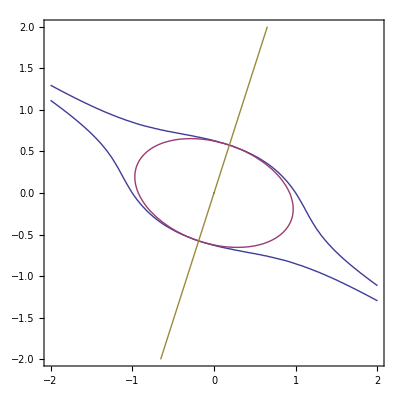

```mathematica
PlotTest[1,2,3,4]
```

```mathematica
Discriminant[a x^3+b x^2+c x+d,x]
```

b^2 c^2-4 a c^3-4 b^3 d+18 a b c d-27 a^2 d^2

```mathematica
(*la partie tangence orthogonale semble marcher*)
(*On attaque donc la partie bitangence*)
Bitangence[a_,b_,c_,d_]:=Block[{r=x/.NSolve[a x^3+b x^2+c x+d,x], disc= b^2 c^2-4 a c^3-4 b^3 d+18 a b c d-27 a^2 d^2,
pos,Chg,Theta},
If[disc>0,(*trois racines réelles, trouver les deux plus proches sur P1R*)
Theta = ArcTan/@r; Theta=Theta-RotateLeft[Theta]; Theta=Abs[Mod[#+Pi/2,Pi]-Pi/2]&/@Theta;
pos=Ordering[Theta]/.{1->3,2->1,3->2};
r=r[[pos]];
,
(*une racine réelle, deux complexes*)
pos=Ordering[Abs[Im[#]]&/@r]; (*on met en premier la racine réelle*)
r=r[[pos]];
];
Chg={{r[[1]]*r[[2]]+r[[1]]*r[[3]]-2*r[[2]]*r[[3]],Sqrt[3]*r[[1]]*(r[[2]]-r[[3]])},{2*r[[1]]-r[[2]]-r[[3]],Sqrt[3]*(r[[2]]-r[[3]])}};
If[disc<0,Chg=Chg.{{1,0},{0,I}}];
Chg=-Re[Chg]*Abs[a^3/(2 disc)]^(1/3);(**2^(-1/3.)/Abs[disc]^(1/3);*)
Return[Chg];
];


(*la matrice de passage semble bonne. Cf fichier 'Test' dans ce même dossier.*)
```

```mathematica
Det[{{r[1]*r[2]+r[1]*r[3]-2*r[2]*r[3],Sqrt[3]*r[1]*(r[2]-r[3])},{2*r[1]-r[2]-r[3],Sqrt[3]*(r[2]-r[3])}}]
```

```mathematica
Factor[-2 √3 r[1]^2 r[2]+2 √3 r[1] r[2]^2+2 √3 r[1]^2 r[3]-2 √3 r[2]^2 r[3]-2 √3 r[1] r[3]^2+2 √3 r[2] r[3]^2]
```

-2 √3 (r[1]-r[2]) (r[1]-r[3]) (r[2]-r[3])

```mathematica
Det[{{r1*r2+r1*r[[3]]-2*r[[2]]*r[[3]],Sqrt[3]*r[[1]]*(r[[2]]-r[[3]])},{2*r[[1]]-r[[2]]-r3,Sqrt[3]*(r2-r3)}}];
```

Part::partd: Part specification r ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification r ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification r ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

```mathematica
Pol[a_,b_,c_,d_,{x_,y_}]:=a x^3+ b x^2 y+c x y^2+ d y^3;
```

```mathematica
TestAlg[a_,b_,c_,d_]:=Expand[Pol[a,b,c,d,Bitangence[a,b,c,d].{x,y}]]; (*on tombe sur x(x^2+3y^2)*)
```

```mathematica
Manipulate[TestAlg[a,2,3,4],{a,1,10}]
```

```mathematica
Manipulate[TestAlg[a,0,-1,0],{a,1,10}]
```

```mathematica
PlotTest2[{a_,b_,c_,d_},range_]:=Block[{Chg=Inverse[Bitangence[a,b,c,d]],Sym, disc= b^2 c^2-4 a c^3-4 b^3 d+18 a b c d-27 a^2 d^2},
Sym=Transpose[Chg].Chg;
If[disc<0,Sym=2^(1/3)*Sym];(*{{5/3,0},{0,1}}*)
ContourPlot[{Abs[a x^3+b x^2 y+c x y^2+d y^3]==1,{x,y}.Sym.{x,y}==1},{x,-range,range},{y,-range,range}]];
```

```mathematica
PlotTest2[P_,range_]:=PlotTest2[(Coefficient[P,#]&/@{x^3,x^2 y,x y^2,y^3}),range];
```

```mathematica
Manipulate[PlotTest2[(Cos[theta1] x-Sin[theta1] y)*(Cos[theta2] x-Sin[theta2] y)*(Cos[theta3] x-Sin[theta3] y),Exp[range]],{theta1,0,Pi},{{theta2,Pi/3},0,Pi},{{theta3,2Pi/3},0,Pi},{range,1,4}]
```

```mathematica
Manipulate[PlotTest2[(Cos[theta1] x-Sin[theta1] y)*(Cos[theta2]^2 x^2+ Sin[theta2]^2 y^2),Exp[range]],{theta1,0,Pi},{{theta2,Pi/3},0,Pi/2},{range,1,4}]
```

```mathematica
PlotTest3[{a_,b_,c_,d_},h_,range_]:=Block[{Chg=Inverse[Bitangence[a,b,c,d]],Sym, disc= b^2 c^2-4 a c^3-4 b^3 d+18 a b c d-27 a^2 d^2},
If[disc<0,Sym=Transpose[Chg].{{(4+h^3)/(3h^2),0},{0,h}}.Chg,Sym=Transpose[Chg].{{(4-h^3)/(3h^2),0},{0,h}}.Chg];
ContourPlot[{Abs[a x^3+b x^2 y+c x y^2+d y^3]==1,{x,y}.Sym.{x,y}==1},{x,-range,range},{y,-range,range}]];
```

```mathematica
PlotTest3Pol[P_,h_,range_]:=PlotTest3[(Coefficient[P,#]&/@{x^3,x^2 y,x y^2,y^3}),h,range];
```

```mathematica
Manipulate[PlotTest3Pol[(Cos[theta1] x-Sin[theta1] y)*(Cos[theta2]^2 x^2+ Sin[theta2]^2 y^2),h,Exp[range]],{theta1,0,Pi},{{theta2,Pi/3},0,Pi/2},{range,1,4},{{h,2^(1/3)},0,2}](*2^(2/3)*)
```

```mathematica
Manipulate[PlotTest3Pol[(Cos[theta1] x-Sin[theta1] y)*(Cos[theta2] x-Sin[theta2] y)*(Cos[theta3] x-Sin[theta3] y),h,Exp[range]],{theta1,0,Pi},{{theta2,Pi/3},0,Pi},{{theta3,2Pi/3},0,Pi},{range,1,4},{{h,1},0,1}]
```

```mathematica
(*on s'occupe maintenant d'identifier rmax pour la première forme*)
RMax[a_,b_,c_,d_]:=Block[{Pt=NearestPoint[a,b,c,d],U, Chg=Bitangence[a,b,c,d], alpha, beta},
U={Pt[[1]],{-Pt[[1,2]],Pt[[1,1]]}}; (* la matrice orthogonale*)
U=U.Chg;
alpha=(Transpose[U].{{Pt[[2]]^(-2),0},{0,0}}.U)[[2,1]];
beta=(Transpose[U].{{0,0},{0,1}}.U)[[2,1]];
Return[-alpha/beta];
];
(*on veut savoir quand on passe de tangent orthogonal à bitangent*)
```

```mathematica
RMax[1,0,-3,0]
```

1.

```mathematica
RMax[1,2,3,4]
```

0.834641

```mathematica
PlotTestRMax[{a_,b_,c_,d_},range_]:=Block[{Pt=NearestPointT[a,b,c,d],U,Sym,Sym2,Dte,R=RMax[a,b,c,d]},
U={Pt[[1]],{-Pt[[1,2]],Pt[[1,1]]}}; (* la matrice orthogonale*)
Sym=Transpose[U].{{Pt[[2]]^(-2),0},{0,R}}.U;
Sym2=Transpose[U].{{Pt[[2]]^(-2),0},{0,Pt[[2]]^(-2)}}.U;
Dte=Pt[[1]];

ContourPlot[{Abs[a x^3+b x^2 y+c x y^2+d y^3]==1,{x,y}.Sym.{x,y}==1,{x,y}.Sym2.{x,y}==1,Det[{{x,y},Dte}]==0},{x,-range,range},{y,-range,range}]];
PlotTestPol[Pol_,range_]:=PlotTest[(Coefficient[Pol,#]&/@{x^3,x^2 y,x y^2,y^3}),range];
```

```mathematica
(*on est dans les choux*)
```

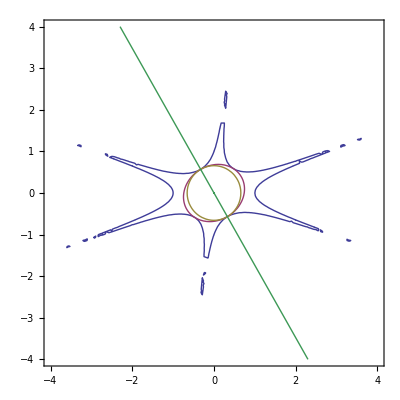

```mathematica
PlotTestPol[x^3-8x y^2+y^3,4]
```

```mathematica
Manipulate[PlotTestPol[(Cos[theta1] x-Sin[theta1] y)*(Cos[theta2] x-Sin[theta2] y)*(Cos[theta3] x-Sin[theta3] y),Exp[range]],{theta1,0.1,Pi},{{theta2,Pi/3},0,Pi},{{theta3,2Pi/3},0,Pi},{range,1,4}]
```

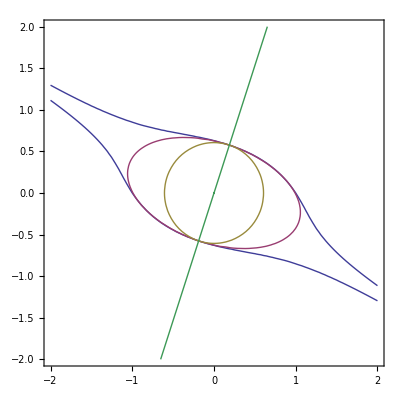

```mathematica
PlotTest[{1,2,3,4},2]
```

```mathematica
(*phase suivante : résolution de l'équation en h, dans la phase bitangente*)
hVal[{a_,b_,c_,d_},r_]:=Block[{Pt=NearestPoint[a,b,c,d],U, Chg=Bitangence[a,b,c,d], alpha, beta, lambda,hMin,bounds, disc= b^2 c^2-4 a c^3-4 b^3 d+18 a b c d-27 a^2 d^2,sdisc,hRes,Sym},
(*Première étape : identification des bornes sur h, cela servira dans le cas de plusieurs racines réelles*)
(*on commence donc par la même idée que RMax*)
U={Pt[[1]],{-Pt[[1,2]],Pt[[1,1]]}}; (* la matrice orthogonale*)
U=U.Chg;
alpha=(Transpose[U].{{Pt[[2]]^(-2),0},{0,0}}.U);
beta=(Transpose[U].{{0,0},{0,1}}.U);
lambda=-alpha[[2,1]]/beta[[2,1]];
hMin= alpha[[2,2]]+lambda beta[[2,2]];
(*vérification*)
(*Return[{hMin,(4+hMin^3)/(3 hMin^2),(4-hMin^3)/(3 hMin^2),alpha[[1,1]]+lambda beta[[1,1]]}];*)
(*bornes admissibles pour la valeur de h*)
If[disc>0,bounds={hMin,1},bounds=Sort[{hMin,2^(1/3)}]];
Sym=Transpose[Chg].Chg/r^2;
(*maintenant on résoud l'équation*)
sdisc=Sign[disc];

hRes=h/.Solve[(4-sdisc h^3 - 3h^2 Sym[[1,1]]) (h-Sym[[2,2]])-3h^2Sym[[2,1]]^2==0,h];
 hRes=Select[hRes,bounds[[1]]≤#≤bounds[[2]]&];
If[Length[hRes]≠1,Print["not a bitangent radius"];Return[hRes]];
hRes=hRes[[1]];Chg=Inverse[Chg];
Return[Transpose[Chg].{{(4-sdisc hRes^3)/(3hRes^2),0},{0,hRes}}.Chg];
];
```

```mathematica
(*vérification : bien*)
```

```mathematica
1<2<3
```

True

```mathematica
hVal[{1,2,3,4},0]
```

{1.83617,1.00753,-0.216588,1.00753}

```mathematica
hVal[{1,0,-8,0},0]
```

{0.763143,2.54381,2.03505,2.03505}